```mathematica
g=9.81;
x[t_]:=x0+vel*Cos[th+t]*t;
y[t_]:=y0+vel*Sin[th+t]*t-(g*t^2)/2;
vel=0;
x0=5;
y0=100;
th=0;

{xmin,xmax}=#[{x[t],0≤t≤10},t]&/@{MinValue,MaxValue}

(*{5,5}*)

{ymin,ymax}=#[{y[t],0≤t≤10},t]&/@{MinValue,MaxValue}

(*{-390.5,100.}*)

Animate[Graphics[{PointSize->0.05,Point[{x[t],y[t]}]},PlotRange->{{Floor[xmin-5,10],Ceiling[xmax+5,10]},{Floor[ymin-5,10],Ceiling[ymax+5,10]}},Frame->True,AspectRatio->1],{t,0,10}]
```

{5,5}

{-390.5,100.}

```mathematica
Manipulate[Show[{ParametricPlot3D[{{100 t,80 t-16 t^2,60 t},{500-200 t,80 t-16 t^2,t+2}},{t,0,tt},PlotRangePadding->20,PlotRange->{{-1500,1000},{-800,100},{0,600}}],Graphics3D@Sphere[{100 tt,80 tt-16 tt^2,60 tt},15],Graphics3D@Sphere[{500-200 tt,80 tt-16 tt^2,tt+2},15]}],{tt,0.1,10}]
```

```mathematica
proc=WienerProcess[];
SeedRandom[123];
sample=Table[RandomFunction[proc,{0,1,0.01},3]["ValueList"]ᵀ,{6}];

Graphics3D@Table[{ColorData["SolarColors"][RandomReal[]],Tube@Line@sample[[i]]},{i,6}]
```

-Graphics3D-

```mathematica
data=RandomFunction[WienerProcess[],{0,1,.01},500];
sd=data["SliceData",1];
cf=ColorData["Rainbow"];
sliced=BarChart[Last[#],Axes->False,BarOrigin->Left,AspectRatio->4,ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{Min[sd],Max[sd]},{0,1}]),ImageSize->70]&[HistogramList[sd,{Range[Min[sd],Max[sd],(Max[sd]-Min[sd])/20]}]];
```

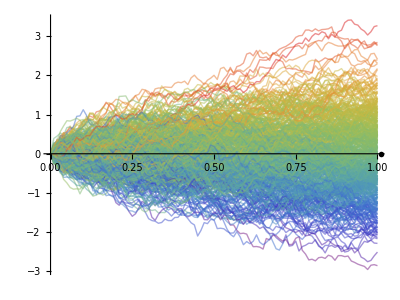

```mathematica
ListLinePlot[data,ImageSize->400,PlotRange->All,AspectRatio->3/4,Epilog->Inset[sliced,{1.01,0},{0,10}],PlotStyle->(cf/@Rescale[sd]),BaseStyle->Directive[Thin,Opacity[0.5]],PlotRangePadding->{{0,.25},{.5,.5}}]
```

```mathematica
rnorms1=RandomVariate[NormalDistribution[0,1],20]
rnorms2= RandomVariate[NormalDistribution[0,1],20]
```

{0.769524,-0.248886,-0.817241,-1.67012,-0.922347,-1.19763,-0.281904,-0.638067,0.796079,0.42937,-0.127914,0.390763,-0.182881,-0.15577,0.999527,0.399033,-1.8699,-0.252312,-0.17633,-1.49085}

{-0.795121,-2.8913,0.056452,-0.450898,-0.648172,0.570463,0.485993,0.217066,0.670078,-0.957108,-1.15058,0.5499,0.569328,0.276037,1.21701,-0.899406,1.1731,-1.12528,-0.83044,0.840118}

```mathematica
rnorms1-rnorms2
```

{1.56464,2.64242,-0.873693,-1.21922,-0.274175,-1.76809,-0.767897,-0.855133,0.126001,1.38648,1.02266,-0.159137,-0.752209,-0.431807,-0.217481,1.29844,-3.04299,0.872968,0.65411,-2.33097}

```mathematica
NormalDistribution
```

```mathematica
max=1000;
coords=Table[{i,RandomReal[]},{i,max}];

Animate[ListPlot[coords[[1;;n]],PlotMarkers->{Automatic,Small},Joined->True,PlotRange->{{0,max},{0,1}}],{n,1,max,1}]
```

```mathematica
sizeOfalk:=10000
rands=RandomVariate[PoissonDistribution[5],10000]
(*rands=RandomVariate[NormalDistribution[2,.65],10000]*)

(*randsNornnalized=rands*(2*π)/10*)
randsNornnalized=rands*(2*π)/10
```

{8,7,4,4,7,7,5,3,7,3,7,3,3,5,1,4,4,1,4,2,4,5,5,7,1,2,4,4,5,7,5,4,7,8,6,4,5,7,3,6,6,1,5,6,5,5,7,3,6,3,7,5,6,8,3,5,6,6,9,2,3,5,5,6,4,4,5,4,3,7,9,4,6,5,6,7,6,5,2,5,7,4,6,3,5,5,6,6,1,7,2,3,5,9,3,4,3,6,7,6,8,6,2,6,1,7,3,7,3,7,5,5,3,2,2,2,5,4,2,6,1,6,6,11,2,4,6,11,5,7,3,4,1,5,5,10,5,7,2,6,6,4,6,3,7,3,7,3,4,4,2,3,6,4,8,6,8,3,4,4,8,8,4,4,6,2,1,9,9,7,7,13,3,4,4,5,6,4,6,4,5,5,7,3,2,4,6,5,8,2,3,4,6,2,4,4,4,11,5,5,8,3,7,7,7,9,4,3,8,9,6,1,6,2,5,5,8,6,2,4,6,3,5,4,4,4,5,5,13,7,4,6,8,6,7,5,3,4,2,4,3,3,4,11,2,4,4,4,5,4,3,5,3,2,7,3,5,9,5,5,2,6,2,6,5,5,4,5,3,5,5,7,3,1,8,5,4,1,6,3,6,6,5,4,7,2,1,4,6,4,1,9,4,3,2,9,5,6,2,6,3,6,5,8,4,2,5,7,4,5,4,4,9,7,7,7,5,5,5,10,3,8,8,6,6,4,5,4,1,3,2,5,5,2,4,4,4,2,4,3,8,10,4,4,4,5,7,5,4,6,8,8,2,3,6,6,5,6,4,4,1,5,5,3,2,4,5,2,1,6,6,4,2,4,5,3,4,7,6,6,3,9,4,2,6,3,4,7,4,6,3,5,3,3,2,3,4,6,8,5,8,5,6,4,5,8,4,7,7,2,4,5,4,3,3,6,3,2,2,7,5,2,3,8,6,3,3,4,6,4,7,7,3,4,2,5,5,3,8,2,10,3,5,9,4,7,5,4,5,10,7,9,5,8,4,3,1,5,7,2,7,10,1,13,7,5,2,9,4,3,1,4,1,2,4,4,8,5,6,5,4,4,5,6,3,7,9,5,7,3,8,9,5,6,5,4,3,1,7,5,5,4,3,8,2,11,7,5,5,2,11,3,7,8,4,2,12,4,4,5,3,5,3,9,2,5,6,8,2,4,4,6,3,2,5,4,4,5,10,5,5,8,5,6,8,4,7,3,4,2,4,4,5,5,4,2,1,2,4,4,2,8,9,11,6,2,8,7,3,4,8,8,6,5,7,7,4,6,8,8,7,6,4,4,4,6,0,4,5,7,4,1,9,4,5,5,3,2,3,5,5,6,3,3,6,5,4,4,8,6,3,4,4,5,5,2,5,5,1,7,4,8,6,5,6,2,7,10,3,7,2,4,1,5,8,2,9,7,3,7,2,3,6,8,5,3,3,10,7,7,2,6,5,6,7,8,8,9,6,8,3,2,7,6,4,3,4,5,6,4,5,6,5,2,3,4,4,6,5,3,9,3,6,6,5,4,5,2,6,9,3,2,6,7,4,7,2,3,4,4,6,5,5,6,5,14,6,5,7,5,3,8,4,7,2,2,3,3,7,3,4,4,9,6,5,3,5,9,6,5,7,3,8,9,2,3,9,6,4,6,4,4,5,9,2,1,4,3,7,7,7,3,6,8,4,2,4,6,4,6,3,5,6,6,8,6,2,3,4,4,2,7,7,6,8,8,4,3,6,6,6,8,5,5,10,4,5,5,5,5,7,4,5,9,7,6,1,5,3,8,3,5,2,4,7,10,2,1,3,4,5,2,7,6,6,6,8,8,7,2,6,4,3,4,4,5,3,11,4,9,6,2,3,4,5,5,6,3,6,10,2,6,3,2,6,6,5,5,4,2,7,9,7,6,6,2,6,6,3,3,8,4,4,4,5,8,3,3,6,7,5,3,6,2,5,5,4,7,7,3,7,5,3,3,5,8,3,6,8,4,4,2,6,7,7,9,5,4,7,6,6,8,7,7,6,6,5,7,9,7,4,5,8,2,2,3,7,4,5,4,4,9,3,4,4,3,9,6,5,4,8,7,7,3,8,4,7,7,6,6,5,4,3,7,3,6,7,4,5,8,7,2,7,4,3,4,7,4,8,10,4,6,4,9,6,3,4,4,6,3,5,4,7,4,2,7,3,1,6,6,3,2,4,8,7,10,6,7,9,3,3,4,5,8,4,7,6,4,7,11,4,7,3,6,1,6,7,4,2,4,7,3,9,6,4,10,4,4,5,6,1,5,2,7,7,2,4,4,8,7,3,5,7,0,2,8,8,6,7,6,3,6,3,4,2,8,5,4,10,5,3,5,4,7,9,6,9,5,3,5,2,7,4,7,6,8,5,8,3,5,7,3,5,8,8,4,5,4,6,2,6,3,4,3,4,9,5,4,7,3,4,4,2,6,5,8,3,3,7,3,5,3,3,5,4,6,5,2,5,4,0,1,7,6,5,4,9,3,6,8,2,5,6,5,3,8,7,4,5,6,6,7,7,2,5,8,7,3,2,5,5,5,5,3,5,5,4,7,7,4,2,2,9,6,1,4,6,7,2,4,5,6,8,5,4,4,4,3,7,6,5,5,8,10,4,5,4,6,2,4,5,4,5,7,2,4,4,3,6,4,4,13,5,2,10,5,8,2,2,6,5,9,4,8,0,3,1,2,5,5,10,10,6,2,4,6,4,2,4,4,2,3,5,5,10,7,4,3,4,4,3,4,5,7,5,5,4,4,6,2,6,6,5,3,5,4,7,3,2,6,5,4,3,2,4,4,5,3,10,8,3,5,3,4,7,6,5,4,3,5,5,5,7,5,7,1,1,4,9,7,5,3,4,3,4,6,8,7,10,3,6,3,4,10,4,4,4,6,7,4,4,5,5,4,5,3,9,5,4,7,4,6,2,1,6,6,4,4,6,12,2,4,0,8,4,6,3,5,6,5,3,6,5,11,6,8,3,2,4,6,4,4,7,2,6,4,2,1,4,1,7,10,4,5,4,5,5,7,7,5,11,3,5,6,6,4,3,1,5,0,3,7,5,4,6,3,3,6,7,1,5,5,6,1,5,6,6,4,2,10,6,8,5,4,5,3,2,5,2,5,5,8,3,4,11,7,2,11,5,3,11,6,2,7,3,9,3,9,6,7,1,2,6,6,2,3,5,5,2,8,9,4,7,3,7,6,8,7,6,9,7,4,8,1,5,3,7,5,1,4,7,3,8,7,6,6,7,5,7,7,4,5,6,3,6,6,9,9,4,1,4,2,7,3,2,4,3,3,4,6,6,4,4,6,4,8,3,7,4,3,3,7,3,3,9,4,6,6,2,3,4,4,4,2,4,6,4,4,8,2,5,10,6,7,5,5,8,9,7,4,4,5,6,4,5,4,1,6,13,5,5,10,4,6,6,6,4,4,6,2,8,1,9,4,3,6,0,7,4,4,7,5,4,4,4,5,3,2,4,5,7,6,4,3,10,9,10,4,5,2,1,2,6,8,6,3,12,7,2,9,4,7,1,5,2,4,1,2,4,8,3,6,2,4,3,7,4,7,5,4,4,4,4,9,3,8,6,4,5,2,2,5,8,6,4,3,10,3,7,3,2,5,0,3,6,3,4,3,5,10,7,5,4,3,3,4,4,5,1,9,2,2,6,5,3,3,6,7,3,4,3,4,4,3,3,3,6,6,4,5,6,2,9,10,4,4,6,7,3,11,11,4,2,4,10,11,3,3,4,4,5,8,5,7,4,3,6,6,5,5,6,4,4,5,6,9,7,8,9,7,5,4,6,7,4,4,13,5,2,10,0,3,1,6,8,5,2,7,5,5,6,7,7,6,6,5,6,2,3,3,4,2,2,5,5,7,6,1,1,7,7,4,3,5,4,11,5,9,9,5,6,5,11,3,4,5,9,9,5,6,7,5,4,7,6,1,5,7,7,5,6,6,5,5,2,3,8,4,6,8,8,5,4,6,3,7,7,4,3,7,6,8,8,6,4,8,6,12,7,13,5,2,9,6,6,2,2,5,5,2,7,4,5,5,5,4,4,6,12,6,9,5,3,4,5,3,3,5,8,8,4,4,5,2,4,9,5,3,4,8,4,6,5,9,6,3,5,6,7,7,10,3,6,3,6,4,8,5,3,7,2,1,1,3,6,3,9,5,6,9,0,5,3,3,5,3,9,3,3,6,5,9,5,9,8,5,3,5,5,4,5,7,9,2,3,3,6,3,5,6,4,2,5,6,4,4,2,4,5,8,5,6,9,8,6,4,8,3,3,3,6,6,6,4,1,5,7,4,4,4,7,11,1,2,1,4,4,5,9,6,1,6,8,6,7,6,5,7,5,5,5,5,7,7,4,3,2,4,3,3,9,4,3,6,1,4,2,2,9,5,5,4,4,7,9,6,7,4,4,3,6,4,8,6,3,5,12,5,3,0,7,5,7,1,6,5,7,10,6,2,3,3,6,2,3,1,6,2,5,1,6,4,9,8,9,6,7,5,2,7,3,4,6,3,4,5,3,7,7,6,5,4,4,2,5,11,4,4,5,6,2,8,8,10,3,6,5,4,4,2,7,3,5,5,5,2,9,5,4,5,5,7,7,5,5,1,4,1,6,5,7,2,4,4,4,4,5,9,3,4,9,5,1,6,4,4,7,3,2,5,1,3,5,6,6,4,8,3,2,7,5,4,4,5,7,5,3,4,1,7,4,5,2,5,5,1,3,5,3,5,1,7,10,1,6,7,6,3,5,6,6,4,5,4,4,8,3,11,4,7,3,7,10,10,6,5,1,4,4,4,6,4,6,5,1,5,4,6,4,9,4,4,10,4,2,4,6,4,3,6,3,8,4,5,2,4,11,4,6,7,8,4,5,3,6,5,9,8,6,7,6,3,3,4,3,5,7,2,5,8,6,1,7,4,6,9,6,5,4,9,6,1,6,5,8,5,6,9,7,6,6,5,5,2,6,7,5,5,4,3,2,2,3,9,6,7,7,6,4,6,8,5,5,8,4,6,2,4,3,2,9,5,7,1,4,6,8,3,6,3,1,6,5,4,5,6,5,4,4,3,5,2,5,3,8,2,4,3,10,6,11,7,5,6,4,8,5,1,2,3,3,4,5,5,3,3,3,4,4,6,5,6,3,5,3,3,4,6,5,9,1,5,5,10,6,3,4,5,5,5,5,4,6,6,2,2,1,5,4,1,3,3,8,5,4,5,8,7,7,3,2,1,3,3,4,4,2,6,2,5,6,5,2,12,3,6,5,4,5,5,3,6,7,5,6,5,3,3,8,5,1,4,9,3,6,8,2,2,6,5,3,9,4,3,6,4,5,2,3,5,4,6,3,6,2,6,2,7,3,8,5,5,5,7,3,6,4,3,4,8,7,9,5,6,1,2,6,1,3,6,2,3,7,7,5,6,4,7,5,5,8,8,5,5,6,3,4,2,9,2,6,5,5,10,6,6,6,4,6,8,4,7,8,7,3,2,4,6,1,4,4,8,3,4,0,11,7,5,3,5,4,7,1,4,3,5,5,4,9,6,8,2,2,2,9,6,0,3,6,5,5,10,2,7,6,5,5,4,6,5,3,2,4,1,4,3,4,7,3,10,4,3,2,2,2,2,5,8,2,3,8,3,4,4,8,1,6,2,5,2,8,4,5,8,6,8,5,5,1,5,9,9,4,4,4,8,6,3,6,11,5,4,3,8,9,1,2,3,7,8,2,4,1,6,4,5,2,4,3,4,7,4,2,7,5,2,9,3,0,8,3,2,6,8,5,7,5,4,6,8,3,5,5,3,4,11,7,5,3,4,6,6,9,6,9,5,8,5,9,5,3,7,4,8,6,4,3,6,8,8,4,7,5,8,6,0,4,8,6,5,4,6,8,5,5,3,6,3,6,4,2,4,3,6,4,4,7,2,8,5,6,8,3,6,8,1,2,4,8,6,6,4,6,5,8,5,3,8,5,5,5,7,5,8,7,5,6,7,3,5,5,2,6,4,6,5,6,3,5,5,3,9,6,6,4,4,3,6,7,7,9,7,8,5,4,4,9,9,1,5,3,6,4,1,5,4,8,2,4,4,4,6,4,5,4,5,5,1,5,4,9,5,8,9,4,7,9,4,5,6,3,3,5,5,6,5,2,5,4,7,5,6,4,1,3,4,5,5,5,4,0,6,2,8,5,6,8,6,2,4,6,5,6,1,6,5,6,6,9,6,6,4,6,5,4,2,1,7,7,5,7,4,9,4,6,7,5,3,6,7,8,3,6,7,2,5,0,1,4,4,8,6,3,2,9,5,6,8,6,6,7,5,5,2,5,6,6,5,2,5,8,6,9,3,4,4,8,6,5,5,5,3,6,4,2,5,10,5,3,3,4,5,2,1,9,4,2,4,5,8,5,7,5,6,5,7,3,5,7,6,6,7,3,6,6,5,5,2,2,2,1,3,2,4,6,3,7,5,4,11,2,8,4,7,5,4,6,4,8,1,5,5,7,2,4,6,6,7,6,7,2,6,3,2,6,2,8,6,3,6,3,7,6,7,4,6,7,4,1,4,5,5,9,7,4,4,6,6,10,6,4,5,5,9,6,5,3,2,2,8,3,4,1,6,4,4,3,4,5,3,2,3,8,6,10,8,4,7,4,6,6,7,9,5,2,3,8,3,5,2,2,4,5,5,3,3,3,5,7,1,8,8,2,5,4,6,7,5,2,2,6,1,1,6,4,12,3,9,9,4,7,5,2,6,6,5,5,9,4,5,1,3,3,5,3,4,6,7,3,6,5,3,3,7,3,3,3,5,6,6,4,6,7,7,2,3,5,7,7,2,4,6,4,5,6,7,4,2,9,5,10,4,5,9,7,5,5,6,4,6,5,5,6,2,4,8,2,5,1,3,0,3,9,6,2,7,6,1,5,8,3,7,8,4,2,5,8,7,8,3,4,5,7,5,1,10,6,6,4,2,4,9,5,4,4,3,3,5,4,7,8,4,8,3,6,7,7,4,2,4,5,4,2,3,5,5,6,8,5,3,4,3,4,5,5,6,4,2,8,6,6,0,8,1,7,4,5,6,10,10,5,5,4,2,6,5,4,3,10,2,2,5,4,6,3,5,7,9,7,4,5,10,6,3,5,8,4,3,4,5,2,7,6,5,6,6,7,10,4,6,4,4,5,6,8,0,1,7,9,7,5,9,9,9,3,3,7,7,7,1,5,4,5,2,2,6,7,4,5,9,3,3,11,7,5,4,3,5,5,4,7,5,8,6,13,6,8,6,6,4,4,8,6,6,4,6,1,3,7,5,7,5,10,5,1,4,4,7,3,6,2,2,5,7,5,3,8,7,6,0,2,2,4,4,8,3,5,8,10,3,8,9,2,3,1,7,11,4,4,5,10,8,5,6,3,6,8,2,6,10,11,2,4,8,4,6,5,7,7,3,4,3,2,6,8,1,3,4,5,3,4,5,5,5,7,11,4,8,2,3,6,7,4,5,3,2,3,8,6,3,7,5,5,4,5,5,7,2,5,5,4,4,2,6,4,3,2,2,7,5,5,5,9,7,2,3,4,3,7,5,5,9,5,3,1,6,2,4,5,4,7,6,8,7,7,7,10,6,4,4,3,8,3,3,5,5,4,4,6,8,8,3,4,5,5,6,6,3,5,6,11,3,4,3,1,3,4,6,6,6,0,4,7,5,3,12,2,6,6,3,2,6,4,4,4,5,5,7,6,3,6,5,8,7,2,8,1,5,4,6,5,5,2,6,5,2,3,5,7,6,5,2,11,3,7,7,3,5,9,7,5,4,4,8,2,2,2,5,5,5,5,3,4,1,4,5,7,3,8,3,9,5,6,5,8,4,9,9,7,9,4,9,3,1,7,5,4,5,6,8,5,7,9,4,6,9,4,3,5,6,3,3,3,3,1,5,4,5,2,5,9,4,4,4,3,3,8,3,4,3,6,5,6,6,5,6,5,9,6,6,5,5,5,7,3,2,1,6,3,3,2,5,3,5,7,9,8,5,8,4,3,3,6,4,3,2,5,3,4,7,2,2,2,5,4,2,1,4,7,5,7,4,9,7,3,6,9,7,6,6,3,2,3,7,4,2,3,2,6,4,3,6,8,3,6,4,7,4,1,6,6,9,4,9,3,5,4,2,1,2,7,4,3,5,4,6,2,5,8,2,3,4,7,8,6,7,6,3,3,4,8,5,5,1,2,6,6,2,4,7,8,4,6,7,6,5,4,7,6,6,6,9,6,5,3,9,7,5,1,8,4,4,5,7,6,5,6,2,5,6,4,2,3,4,3,1,6,6,7,3,4,6,5,3,6,3,2,3,5,5,5,2,9,4,5,4,6,6,7,5,2,2,3,6,5,4,6,3,7,8,3,7,4,5,3,3,3,7,3,4,7,5,6,2,6,4,4,2,5,4,5,3,3,5,6,2,5,3,5,3,4,5,2,9,3,7,2,2,6,6,4,5,2,8,5,3,2,4,5,4,6,7,2,3,8,5,4,6,5,4,3,3,6,4,3,2,3,5,3,3,4,5,4,4,8,6,2,6,4,4,5,12,8,4,9,3,3,2,4,4,7,4,3,5,4,4,8,2,4,4,8,1,4,6,8,4,6,2,5,4,7,6,8,3,5,2,4,6,3,4,2,4,5,1,5,5,3,3,3,8,3,6,7,4,2,3,4,6,4,2,2,4,7,6,8,5,6,6,1,0,2,3,8,7,4,6,4,10,7,5,7,9,3,5,3,6,5,3,8,5,1,4,4,3,4,12,6,3,4,4,6,6,8,4,3,2,7,4,2,4,6,5,7,5,4,4,4,3,6,6,2,4,4,3,8,6,5,5,2,4,6,3,6,5,3,4,4,7,4,6,6,6,2,8,3,2,9,5,2,3,1,4,6,5,7,3,0,9,3,4,3,5,7,5,4,6,4,4,8,4,5,6,2,3,4,5,6,1,7,9,6,5,6,2,5,7,3,4,5,5,1,2,5,3,5,4,3,3,7,4,9,6,5,5,4,5,10,2,6,5,2,2,4,7,3,2,3,3,5,8,8,4,11,7,3,7,7,7,6,5,4,3,5,6,4,5,3,5,6,11,7,1,7,10,5,4,4,8,4,2,3,7,8,3,5,5,5,5,4,4,5,6,5,4,12,3,8,12,4,3,2,6,2,3,2,7,7,4,4,6,9,6,12,6,3,5,5,3,7,5,5,7,0,2,10,10,6,3,6,3,7,7,4,4,7,8,5,6,10,3,3,6,8,4,6,10,11,6,5,5,3,5,4,3,7,7,8,6,5,4,4,4,2,3,6,4,7,2,6,2,6,5,6,6,5,10,2,4,7,5,5,3,4,2,9,3,8,5,3,2,4,4,5,6,8,6,7,8,6,3,3,8,7,6,4,2,8,7,6,6,2,3,6,11,4,7,6,3,7,1,3,8,3,4,7,2,8,5,5,3,5,5,4,4,4,4,4,3,6,6,4,7,4,3,5,5,4,4,5,3,9,5,3,7,4,5,4,8,4,7,3,3,6,9,3,2,9,6,4,6,2,3,3,5,4,7,3,7,4,7,4,5,6,7,8,6,3,4,7,2,6,5,5,4,8,5,2,8,5,7,6,2,3,3,5,8,7,5,4,6,3,4,9,7,6,1,5,6,4,2,7,5,3,6,4,9,2,6,8,2,2,5,5,2,4,9,6,8,4,1,4,3,8,4,5,3,5,7,5,1,7,10,6,1,6,12,6,1,8,10,2,7,5,3,5,2,5,4,6,3,8,2,3,6,4,3,7,2,3,5,3,7,4,6,5,7,10,8,3,7,4,5,3,7,5,3,0,5,5,4,8,3,4,4,4,3,4,5,6,8,6,6,3,11,8,7,5,2,4,6,3,1,4,3,11,2,1,6,5,7,7,6,3,9,8,2,6,3,9,6,4,5,8,5,4,2,2,5,4,5,9,9,4,4,4,7,6,4,2,7,4,3,4,7,4,4,5,7,8,8,7,14,3,1,9,4,6,5,5,3,5,7,7,4,8,8,7,1,8,6,7,0,5,2,2,3,3,4,8,9,4,6,4,6,4,4,12,5,6,4,7,5,7,6,3,7,7,11,8,2,3,8,3,9,3,5,2,7,5,4,1,8,6,1,3,7,8,3,3,3,4,2,3,8,1,6,3,5,6,6,4,2,2,5,3,8,2,5,11,8,4,7,8,7,5,6,4,5,9,5,5,6,6,6,4,7,8,3,4,4,3,5,4,4,4,1,4,3,6,0,0,4,1,5,7,6,5,3,5,5,7,5,5,5,1,8,3,1,3,6,3,2,4,5,3,4,5,4,2,6,5,1,5,6,6,4,6,5,3,2,8,5,6,3,8,2,5,4,4,9,5,8,10,5,7,6,6,7,3,8,9,4,2,6,1,6,4,6,5,6,8,7,6,4,2,6,6,4,4,3,1,5,5,5,5,7,5,3,5,4,6,2,6,4,4,5,5,5,9,4,4,8,2,2,6,5,9,4,1,6,7,5,7,6,7,3,3,3,5,3,4,4,3,5,6,4,4,8,4,4,10,3,1,4,4,4,7,9,4,4,5,3,7,5,4,5,9,5,7,2,1,4,7,1,9,4,4,2,4,7,3,3,9,4,6,3,10,4,5,4,4,2,6,3,3,6,3,6,3,2,3,3,1,2,3,11,6,8,6,7,7,3,6,8,6,7,4,6,8,3,5,8,4,4,2,6,5,6,2,4,5,3,4,4,7,3,3,4,5,5,8,6,4,7,6,5,2,3,1,8,3,2,5,2,4,4,5,3,4,8,12,14,3,4,5,4,4,3,4,3,5,7,4,7,6,5,8,6,6,4,8,5,2,3,6,3,11,5,6,1,7,4,3,7,5,4,12,4,5,6,3,6,6,1,4,1,4,3,7,5,3,7,9,2,3,2,3,7,2,6,7,5,4,4,8,8,4,5,6,1,6,6,7,7,4,7,2,3,3,1,2,4,3,3,3,3,10,3,5,3,8,2,7,4,7,4,4,6,4,7,6,6,6,6,5,5,2,4,6,3,8,4,6,5,4,3,5,4,5,6,5,10,7,4,2,4,2,3,3,2,4,4,4,5,6,3,9,6,2,10,5,6,5,6,3,3,3,2,5,1,4,6,5,6,3,10,5,2,5,7,10,1,9,8,8,5,9,6,5,4,5,7,8,3,4,7,4,5,6,3,5,11,5,11,5,4,6,6,4,3,3,2,6,4,5,4,3,7,6,3,3,4,6,5,7,9,4,7,3,3,4,4,3,5,5,3,6,3,1,7,4,3,11,2,6,4,5,9,3,4,4,7,10,0,4,4,2,5,4,2,4,3,6,9,1,2,5,5,6,3,3,7,7,7,6,5,4,11,6,4,4,10,5,4,3,6,10,4,4,7,4,4,7,5,8,3,3,3,3,5,2,5,2,2,6,5,6,3,2,8,4,5,6,3,1,7,5,11,7,4,0,5,4,8,3,4,5,4,2,4,4,3,9,5,4,3,4,6,3,3,10,4,7,5,7,1,2,3,4,5,8,2,4,1,13,3,6,6,4,1,2,9,5,8,5,3,5,7,7,3,4,5,7,4,1,5,4,3,5,4,7,6,4,6,7,6,2,3,6,5,1,4,11,6,5,6,5,5,3,3,4,4,2,4,2,5,4,8,7,4,5,4,6,5,5,6,4,5,6,2,4,5,4,4,9,4,1,4,2,4,4,8,4,4,4,4,7,9,5,7,4,6,4,1,7,5,3,5,3,3,5,2,4,3,5,4,6,7,5,4,1,5,6,2,4,3,3,7,3,8,3,8,5,6,6,5,4,6,4,5,7,3,2,5,5,5,6,3,5,5,3,3,3,5,3,5,5,10,7,4,5,11,9,5,2,7,8,7,2,3,3,4,2,6,6,1,3,4,7,1,4,3,4,5,3,8,8,6,4,2,3,2,8,7,2,6,5,3,9,7,3,4,4,5,2,3,3,3,2,5,5,2,10,6,4,5,12,5,2,10,2,3,3,4,7,5,7,5,3,3,3,1,2,4,4,2,4,6,5,8,3,5,10,8,3,6,6,4,5,4,7,5,0,2,8,3,3,5,6,4,2,9,5,4,4,2,4,3,3,2,4,3,3,7,3,8,5,2,0,4,6,4,7,4,5,8,3,2,4,7,3,10,2,9,6,2,3,2,7,4,3,8,5,4,3,7,6,11,0,6,2,3,3,8,0,9,8,4,3,2,6,5,7,3,5,5,4,8,4,3,6,6,5,2,3,4,7,5,10,8,3,1,3,2,6,6,4,6,6,4,4,1,7,8,5,3,7,6,2,6,5,4,7,7,5,3,4,4,6,3,5,5,4,6,7,6,3,6,7,11,12,3,7,7,3,2,3,4,9,6,6,6,2,4,7,3,4,3,6,2,3,6,8,7,5,6,7,10,4,4,5,5,6,4,3,2,4,4,5,11,3,9,5,4,4,2,6,3,3,3,10,1,5,2,1,7,9,8,5,6,6,4,4,5,3,4,7,2,9,4,8,5,2,6,6,5,2,5,1,3,5,6,6,1,5,10,6,5,7,10,5,9,1,3,5,6,2,2,8,5,5,9,8,7,7,7,7,6,6,4,5,3,9,3,3,3,0,2,6,8,4,6,4,4,2,10,4,5,6,3,5,5,9,6,7,10,2,4,3,4,4,2,4,6,7,9,6,5,10,3,3,4,5,2,5,7,3,5,2,7,4,3,6,1,4,2,5,4,4,7,3,5,6,7,5,7,5,5,4,1,6,6,3,7,7,6,3,4,3,4,7,4,5,2,7,9,6,6,4,8,7,8,5,5,5,2,6,3,2,2,2,4,2,6,8,7,4,4,2,4,2,2,6,1,8,9,7,9,4,2,3,7,0,5,1,4,2,10,6,4,7,2,11,6,4,10,8,3,3,4,6,3,5,10,3,2,7,5,9,4,7,5,4,2,2,3,4,6,5,4,4,4,5,4,3,6,2,5,9,4,5,4,6,1,5,4,6,5,5,5,5,5,8,4,7,2,4,6,5,1,3,11,6,4,3,6,6,9,7,5,4,7,5,3,6,1,1,2,5,4,7,6,7,6,14,4,7,2,4,5,6,7,8,5,5,3,3,4,5,3,5,2,5,6,5,5,8,6,5,2,2,5,3,3,3,3,4,6,4,2,5,8,8,4,5,7,6,1,4,7,6,5,1,7,3,7,7,4,2,5,6,6,3,6,2,5,3,3,3,5,4,3,8,3,6,5,4,3,1,6,7,0,2,4,5,7,4,5,5,1,3,3,6,4,6,5,6,9,2,8,4,10,5,5,5,9,7,4,5,6,6,4,2,6,1,1,8,9,5,6,2,9,3,5,10,3,8,9,7,4,4,3,6,4,5,2,2,9,2,3,4,6,4,5,7,4,7,8,7,3,4,5,6,3,3,6,4,4,4,3,5,4,5,3,4,5,3,4,5,5,4,10,5,3,8,4,4,1,2,8,1,2,4,11,7,5,4,3,6,8,3,7,4,7,9,5,6,6,5,3,7,3,9,3,6,6,2,4,7,6,3,7,4,3,5,5,4,5,7,6,4,6,12,6,6,7,4,9,3,6,2,5,8,5,3,2,5,6,8,6,9,3,4,5,4,5,5,4,6,3,3,8,1,6,5,6,5,8,5,5,4,3,4,2,6,4,6,5,5,4,4,4,6,6,3,11,7,7,10,1,5,4,1,4,3,5,4,7,4,3,5,4,5,6,4,1,5,5,4,8,4,7,5,2,7,4,7,3,3,4,5,5,6,5,4,5,5,7,5,2,5,7,2,2,3,5,4,2,6,4,2,12,9,1,3,6,3,6,6,4,5,3,3,2,7,7,6,3,9,7,6,8,6,5,3,2,11,7,6,7,4,3,6,5,5,6,4,3,4,0,8,5,3,4,4,4,4,3,5,5,3,4,5,5,6,2,3,4,4,5,5,3,6,4,8,5,7,5,5,7,8,5,5,6,6,5,6,6,4,8,5,5,7,8,2,12,4,6,5,7,6,5,7,7,2,6,10,3,4,6,3,5,6,4,5,4,7,2,6,4,11,5,3,6,6,4,5,4,1,9,3,12,5,4,4,4,6,8,4,6,3,4,4,8,4,4,3,5,5,6,2,6,4,7,6,4,7,6,5,6,6,4,2,4,3,6,8,2,4,6,6,6,4,6,3,5,4,2,3,4,4,7,6,5,6,4,5,2,5,3,4,3,4,3,7,3,9,4,6,4,5,6,8,5,4,7,6,6,3,2,7,6,5,8,5,6,7,3,4,3,4,4,3,5,5,5,4,4,9,3,6,5,5,3,7,4,7,5,7,6,3,10,7,6,5,3,3,7,5,3,0,6,5,6,3,7,3,9,3,8,5,3,5,5,5,6,6,8,5,5,12,9,3,3,5,4,4,2,10,2,2,5,7,9,2,3,6,8,7,4,6,3,3,9,7,2,5,3,3,5,3,5,5,5,6,4,2,6,9,2,7,6,7,1,6,7,2,5,2,3,3,2,9,7,8,2,4,4,8,9,8,7,5,4,5,5,3,9,10,7,3,5,6,9,3,5,7,10,3,3,7,9,4,3,7,3,7,3,4,5,6,6,1,9,5,5,4,7,7,5,9,6,3,3,3,9,7,8,5,6,7,6,4,13,7,4,3,1,9,2,5,3,5,6,4,9,4,3,1,7,2,4,3,4,6,6,4,1,2,6,8,8,3,5,3,6,5,8,7,7,8,6,4,0,11,4,4,8,6,3,4,3,7,6,6,6,1,5,2,5,7,7,8,4,4,4,4,5,8,9,3,8,4,10,1,8,2,3,7,9,3,6,7,7,8,3,5,10,4,4,9,2,9,5,5,3,6,7,4,6,8,4,6,8,7,3,4,6,10,3,3,9,4,4,4,11,4,1,6,4,5,7,6,4,2,5,6,2,6,5,4,6,8,3,5,6,8,6,2,6,2,7,7,5,6,9,7,5,6,2,3,7,6,7,5,6,6,7,4,11,5,7,4,3,2,4,6,5,4,4,5,3,7,9,6,5,11,6,8,5,3,3,2,7,6,4,0,4,5,7,3,7,7,4,4,5,3,7,4,5,7,2,2,10,2,3,2,8,2,6,2,5,6,5,7,3,5,3,3,4,6,6,7,4,6,5,5,6,2,5,3,2,5,3,4,4,8,5,7,4,3,2,10,6,8,3,6,5,1,4,7,4,1,6,5,3,8,2,4,2,2,5,2,5,6,4,3,4,2,7,8,8,10,5,5,5,4,7,5,8,6,6,6,5,5,6,2,7,7,3,3,7,5,5,5,4,6,3,5,10,3,8,9,7,8,7,3,3,4,5,4,4,5,7,5,5,4,3,7,4,7,8,5,3,4,7,10,4,8,4,9,5,3,3,7,7,8,8,7,3,3,1,3,8,3,3,4,5,9,4,4,4,6,6,2,3,2,4,6,7,4,10,5,3,6,6,4,6,4,2,5,11,3,4,5,5,4,9,7,8,4,8,7,4,8,8,4,3,4,4,4,5,4,3,5,6,4,3,4,2,3,2,9,7,2,7,2,6,2,7,5,5,3,4,6,4,4,6,8,5,3,4,5,4,11,2,5,7,3,6,4,7,2,3,4,8,2,5,7,8,6,2,10,3,6,3,2,8,5,5,8,5,3,3,4,4,8,8,3,4,3,5,4,3,7,5,5,7,2,3,4,7,5,3,2,7,2,8,3,2,7,4,4,9,3,5,5,5,6,3,8,7,4,8,2,3,3,4,5,4,2,0,3,7,4,3,4,10,4,3,11,2,3,8,5,7,6,3,2,6,7,8,2,6,6,6,4,4,4,5,9,6,5,6,5,2,6,3,4,3,4,7,4,4,5,8,4,8,7,9,2,4,6,9,3,4,3,5,6,7,4,6,6,5,6,3,3,6,9,5,4,3,8,5,2,6,6,7,7,4,8,3,5,9,9,5,6,1,6,2,2,5,4,4,3,6,7,5,3,7,10,8,6,7,7,1,3,3,2,6,6,2,7,3,5,7,9,8,5,8,4,3,8,5,4,5,4,6,1,2,2,0,7,7,2,5,4,3,1,6,10,4,5,5,5,8,9,4,3,5,6,7,4,4,4,5,4,3,1,2,6,2,6,8,6,9,4,3,8,7,3,6,5,4,6,4,3,10,9,6,6,4,7,7,6,8,5,2,5,7,1,4,3,7,8,3,5,7,5,6,6,6,5,5,3,3,3,2,4,4,4,4,4,8,4,6,4,4,6,4,7,4,2,5,3,3,4,6,5,6,5,5,12,7,3,4,8,5,3,6,2,7,4,6,8,7,3,4,4,8,4,6,9,6,2,5,6,7,5,6,4,6,7,6,5,7,4,3,3,3,2,3,4,9,4,6,9,5,4,4,2,3,3,6,7,3,5,5,4,4,1,2,5,6,9,2,3,5,4,3,4,6,4,1,6,4,6,2,2,7,8,8,6,4,2,4,5,8,2,7,3,4,4,5,7,4,6,5,5,5,7,3,5,6,7,6,5,5,9,5,5,5,7,4,5,5,6,5,4,4,7,6,5,6,6,9,3,2,9,1,3,6,6,12,3,4,5,3,8,4,3,6,4,0,2,9,4,8,9,5,7,5,2,5,6,6,9,5,4,7,4,7,6,8,6,5,7,7,5,11,11,9,4,4,7,6,3,6,7,6,8,5,5,3,4,6,5,2,3,8,2,6,4,2,9,7,11,4,6,6,7,9,2,6,12,6,5,1,6,7,4,6,4,3,5,4,5,2,9,4,7,3,6,6,6,3,7,4,6,4,6,10,6,5,4,1,6,6,4,3,4,6,4,3,5,3,2,4,10,5,5,8,6,5,5,4,4,9,3,6,6,8,9,8,3,4,2,3,4,3,3,11,8,7,4,3,5,3,11,7,5,5,4,7,5,4,9,3,5,2,4,7,4,5,7,8,7,5,7,5,2,7,4,6,5,8,6,6,6,3,3,12,4,3,11,7,5,7,4,3,4,5,1,6,2,1,5,6,5,3,4,3,9,4,2,3,7,4,8,4,4,5,2,6,7,7,7,7,2,1,6,1,5,5,5,6,3,1,5,4,5,6,0,6,0,6,2,11,7,5,8,6,7,9,4,8,2,6,5,3,6,4,7,4,6,7,3,9,5,2,5,3,4,3,7,5,5,4,3,2,3,4,3,5,4,4,5,11,5,12,2,4,6,4,5,9,5,7,4,7,6,3,5,4,8,5,5,4,5,6,5,5,1,4,4,3,2,11,4,6,5,1,12,6,5,6,6,6,2,4,2,4,7,3,5,7,2,6,6,2,11,3,6,3,7,8,4,2,6,3,6,8,3,6,12,3,6,3,9,4,5,2,8,4,3,4,6,1,4,4,4,4,7,4,8,9,2,6,6,7,3,4,5,5,2,1,8,3,7,5,5,6,6,8,6,6,10,5,4,4,2,6,5,7,6,12,4,6,7,5,6,3,4,4,3,5,8,4,7,8,5,3,1,4,5,5,4,4,3,6,7,6,4,4,7,9,7,5,4,4,8,6,1,7,2,4,2,7,4,8,7,5,6,5,5,3,7,6,5,4,10,5,2,6,5,6,5,7,5,3,8,4,6,12,5,5,2,5,5,7,2,5,5,4,2,4,2,4,12,4,5,2,5,7,6,4,4,5,8,4,12,3,6,4,5,7,7,3,7,4,3,3,8,7,6,6,1,9,5,7,3,3,3,6,8,2,5,4,6,1,4,5,6,5,8,2,10,3,8,6,3,2,3,6,5,10,4,1,3,8,6,4,5,7,3,4,4,3,5,3,4,2,3,5,7,2,4,10,5,10,4,3,6,2,3,4,3,8,4,5,3,4,2,4,8,7,5,9,4,7,4,6,2,4,5,4,2,4,1,2,6,5,8,4,4,8,5,2,3,5,2,7,9,1,10,10,5,4,6,13,5,3,6,3,4,6,5,5,8,6,0,3,8,3,3,6,5,10,8,6,3,7,5,5,7,2,6,3,5,6,3,11,3,7,7,5,5,5,5,6,8,1,2,6,3,5,2,6,5,5,4,1,4,5,9,5,4,8,8,5,6,6,9,3,3,5,2,4,11,7,5,1,5,8,6,6,5,6,5,7,5,8,4,5,3,8,7,9,7,4,7,2,8,1,4,4,2,3,6,6,6,4,10,3,6,6,6,7,6,2,3,5,1,4,4,0,7,4,6,7,6,5,9,4,6,7,6,6,3,4,2,6,2,8,3,4,7,7,6,5,6,9,6,5,5,2,3,5,5,7,7,3,6,7,5,6,5,6,6,6,4,2,0,2,7,6,5,4,6,3,1,8,3,2,7,6,6,4,5,3,6,7,5,5,7,4,5,5,3,3,2,7,4,7,9,5,6,4,7,7,5,8,5,6,5,7,2,3,3,4,6,4,4,4,10,3,6,3,4,4,3,3,1,5,5,5,6,4,6,5,5,8,5,4,6,7,7,6,6,6,10,2,6,9,7,7,5,6,5,6,3,4,8,5,2,6,5,5,5,5,4,4,5,2,3,5,9,6,6,4,7,4,4,7,4,6,4,4,4,3,4,4,5,2,10,5,5,2,2,6,2,13,8,4,3,6,9,3,7,2,6,1,11,4,8,5,8,1,5,8,6,8,8,11,8,6,1,5,8,3,6,8,3,5,7,6,4,6,3,6,4,3,5,2,4,4,8,5,3,0,5,6,4,7,6,3,10,2,5,9,5,0,3,4,4,10,9,4,7,9,6,5,9,6,1,5,2,3,1,4,6,6,4,6,4,6,3,5,3,6,3,2,6,3,10,3,5,5,3,1,5,5,6,2,6,5,7,6,8,4,7,4,3,5,5,6,12,3,5,7,8,6,2,11,10,5,6,6,10,4,3,5,3,4,10,4,3,7,6,9,5,3,5,2,4,2,7,2,8,4,3,7,5,7,3,5,3,5,3,4,5,8,6,4,8,6,2,5,5,6,6,5,4,6,4,5,5,4,6,4,3,5,4,6,1,5,7,7,7,3,5,2,1,3,6,8,9,7,4,6,5,6,8,9,5,4,8,2,2,0,3,6,6,7,3,6,5,5,5,5,3,8,7,9,1,9,6,5,5,8,4,7,6,4,2,6,4,6,4,4,6,6,3,6,4,8,5,7,3,8,2,8,3,6,3,5,11,6,5,6,5,5,9,7,5,5,5,2,5,5,4,7,3,3,5,6,4,6,10,1,5,10,8,2,6,6,6,8,4,4,10,5,1,3,3,3,4,4,5,8,6,3,3,12,2,5,4,10,9,4,2,4,4,3,3,5,3,6,4,6,0,2,10,4,3,7,4,3,3,4,4,4,3,8,4,3,2,3,2,5,4,6,6,3,2,5,2,6,6,5,6,3,6,7,5,10,1,6,7,3,9,7,3,5,5,8,7,5,5,6,3,9,8,5,4,5,2,7,6,8,6,6,7,5,7,3,2,5,7,4,5,6,7,4,8,7,7,3,4,3,2,6,4,4,5,2,3,8,6,1,7,5,4,4,7,5,4,7,5,3,10,4,5,4,4,3,5,4,2,2,8,7,6,6,3,6,7,7,3,4,5,1,4,5,6,6,4,8,6,8,5,4,6,10,6,4,5,4,7,2,5,7,2,3,5,1,5,4,6,6,5,5,3,4,3,4,2,11,9,3,4,4,4,4,4,2,4,5,5,2,7,10,2,8,4,6,9,4,6,5,7,7,7,5,4,2,4,7,6,7,3,4,5,5,3,3,3,3,7,5,1,4,7,6,3,7,2,3,7,7,11,4,6,7,5,5,5,7,8,5,2,9,8,4,2,7,6,1,8,5,4,4,9,3,4,8,6,7,4,1,2,4,6,5,5,7,3,3,4,4,5,3,4,5,4,3,8,3,2,4,6,5,11,5,3,6,6,8,7,2,5,4,10,3,6,6,3,5,8,6,4,6,7,6,2,4,4,2,5,5,3,2,6,5,3,6,5,6,3,5,2,4,5,8,4,5,7,6,7,4,6,1,4,6,4,4,5,4,6,6,5,5,8,2,6,9,4,2,5,5,3,7,5,2,5,8,1,5,2,6,5,3,3,1,5,3,3,4,11,4,2,3,3,6,8,4,7,3,4,10,8,7,5,6,5,6,4,1,7,5,3,2,6,3,5,5,2,4,4,4,6,6,11,6,4,4,10,4,4,4,6,6,5,5,5,5,4,4,4,4,3,2,4,7,4,9,6,2,6,3,2,4,2,3,6,3,9,3,6,5,6,3,4,3,5,5,6,3,2,6,6,2,8,8,5,7,5,4,6,3,5,5,5,6,11,5,5,0,4,7,7,2,6,3,8,4,3,6,5,8,7,2,1,4,4,6,9,3,3,6,3,4,6,3,5,7,4,5,7,4,4,3,5,4,9,4,2,7,1,9,8,6,6,7,2,4,3,3,7,6,3,3,2,6,5,1,4,3,3,10,4,5,2,6,6,4,7,5,2,3,6,3,5,3,9,9,5,8,5,4,6,6,4,8,2,7,5,1,3,5,8,3,8,3,3,3,5,4,1,5,3,6,5,4,3,6,2,4,2,3,5,4,7,4,7,3,11,9,2,9,6,7,5,5,4,7,6,8,4,4,7,1,4,8,5,6,6,9,4,7,8,3,6,4,6,1,7,8,5,9,4,5,4,4,3,7,11,4,7,6,7,5,4,5,5,1,5,6,5,5,4,8,4,4,6,7,5,1,5,5,4,4,5,10,5,5,1,6,8,2,6,6,2,7,7,3,4,3,4,3,0,6,8,3,7,7,5,9,6,3,2,4,6,10,4,8,5,3,2,3,4,8,3,1,6,6,6,4,6,9,3,6,2,6,4,4,5,3,4,1,2,4,7,4,8,6,5,5,5,6,5,2,3,6,10,4,7,5,5,1,9,10,7,4,5,5,2,1,5,4,5,5,6,10,5,2,8,5,5,4,2,6,7,3,7,3,5,6,7,2,3,6,4,5,8,4,6,5,6,4,6,4,3,5,4,6,10,5,4,3,9,3,7,7,1,6,4,4,8,5,4,8,5,6,3,4,8,3,5,3,5,3,5,4,2,5,4,9,10,5,7,6,7,4,5,6,4,5,7,4,4,8,8,7,3,4,6,2,5,5,2,6,9,4,2,7,5,4,5,2,6,5,4,3,6,4,1,7,9,4,3,7,3,8,4,6,6,3,4,4,4,4,4,3,7,3,6,3,2,4,8,4,7,4,3,4,4,7,3,4,3,9,3,4,1,6,2,7,12,5,7,3,4,10,6,4,4,5,7,6,4,3,2,6,7,6,7,6,2,6,4,4,3,1,4,6,2,3,5,6,5,6,3,4,7,4,5,4,4,4,3,4,11,3,5,6,7,6,2,10,2,3,3,8,4,6,4,7,5,5,3,8,2,5,5,8,9,7,3,4,2,3,6,5,10,2,2,3,10,4,7,4,3,6,6,6,4,5,4,2,3,6,6,5,7,6,3,7,3,8,8,4,6,4,12,4,3,6,4,0,5,11,3,5,4,7,6,4,3,5,4,9,0,6,4,5,5,10,3,4,1,5,7,4,3,7,7,6,4,5,2,4,4,7,5,6,3,9,4,3,5,8,5,3,2,5,5,7,5,7,12,8,4,4,9,5,9,8,7,4,6,9,6,4,5,7,5,3,5,3,6,6,9,7,4,2,4,5,4,5,3,1,6,2,10,4,3,4,3,4,6,7,10,5,5,8,10,7,6,6,4,2,5,10,5,6,5,1,5,3,8,8,6,9,4,3,5,8,5,3,2,2,2,3,4,4,5,5,3,8,5,4,4,4,3,8,8,3,3,4,6,5,8,7,6,4,1,4,3,4,7,3,5,6,7,6,4,7,7,8,5,4,5,3,2,4,8,6,4,7,8,7,3,6,6,6,13,7,3,5,5,6,1,6,6,4,6,5,3,1,2,5,7,4,8,4,4,4,6,6,2,4,4,6,6,10,6,5,3,3,4,7,9,7,9,7,4,8,6,6,4,5,1,3,4,5,7,5,9,5,3,6,9,3,3,3,1,3,3,4,12,6,4,3,8,5,4,6,4,8,4,1,3,6,4,0,3,4,6,3,6,5,3,6,4,8,5,8,6,3,7,2,5,4,2,4,5,5,6,6,4,5,5,5,4,6,6,3,7,5,7,2,8,8,8,4,6,7,3,2,5,4,4,5,0,4,2,8,3,6,7,3,7,3,6,8,1,7,7,8,4,4,6,6,5,2,6,5,8,3,2,4,3,5,6,4,2,5,8,6,7,6,5,2,7,2,3,8,3,4,8,5,6,2,5,3,2,5,4,7,5,4,5,2,11,7,7,3,2,7,3,4,8,6,7,4,4,7,6,6,7,2,6,5,3,3,4,5,8,3,6,5,7,7,6,3,6,4,5,2}

{(8 π)/5,(7 π)/5,(4 π)/5,(4 π)/5,(7 π)/5,(7 π)/5,π,(3 π)/5,(7 π)/5,(3 π)/5,(7 π)/5,(3 π)/5,(3 π)/5,π,π/5,(4 π)/5,(4 π)/5,π/5,(4 π)/5,(2 π)/5,(4 π)/5,π,π,(7 π)/5,π/5,(2 π)/5,(4 π)/5,(4 π)/5,π,(7 π)/5,π,(4 π)/5,9936,(2 π)/5,(7 π)/5,(3 π)/5,(4 π)/5,(8 π)/5,(6 π)/5,(7 π)/5,(4 π)/5,(4 π)/5,(7 π)/5,(6 π)/5,(6 π)/5,(7 π)/5,(2 π)/5,(6 π)/5,π,(3 π)/5,(3 π)/5,(4 π)/5,π,(8 π)/5,(3 π)/5,(6 π)/5,π,(7 π)/5,(7 π)/5,(6 π)/5,(3 π)/5,(6 π)/5,(4 π)/5,π,(2 π)/5}
 |  |  |  |

```mathematica
randsNornnalized=Take[randsNornnalized,100]
```

{(7 π)/5,(7 π)/5,(4 π)/5,(3 π)/5,(6 π)/5,(4 π)/5,π,(4 π)/5,π,(2 π)/5,(2 π)/5,π,(7 π)/5,(6 π)/5,π,(2 π)/5,π/5,0,(6 π)/5,(3 π)/5,(4 π)/5,(2 π)/5,(9 π)/5,(7 π)/5,(4 π)/5,(4 π)/5,2 π,(7 π)/5,(6 π)/5,π,(3 π)/5,(8 π)/5,π,π,π/5,(3 π)/5,(2 π)/5,(7 π)/5,(7 π)/5,(6 π)/5,(7 π)/5,(3 π)/5,(2 π)/5,(2 π)/5,(6 π)/5,(9 π)/5,(3 π)/5,(2 π)/5,(3 π)/5,2 π,(3 π)/5,(9 π)/5,π,(4 π)/5,(3 π)/5,(4 π)/5,(3 π)/5,(6 π)/5,(7 π)/5,(3 π)/5,(8 π)/5,(9 π)/5,(3 π)/5,(2 π)/5,(3 π)/5,(8 π)/5,(6 π)/5,(7 π)/5,π,π,(8 π)/5,π,π,(4 π)/5,(3 π)/5,(3 π)/5,(3 π)/5,π/5,π,π,(9 π)/5,(11 π)/5,(4 π)/5,(2 π)/5,(4 π)/5,(2 π)/5,(7 π)/5,(4 π)/5,π,(3 π)/5,(4 π)/5,π,(2 π)/5,(7 π)/5,π,(7 π)/5,(6 π)/5,(3 π)/5,(6 π)/5,(4 π)/5}

{(7 π)/5,(7 π)/5,(4 π)/5,(3 π)/5,(6 π)/5,(4 π)/5,π,(4 π)/5,π,(2 π)/5,(2 π)/5,π,(7 π)/5,(6 π)/5,π,(2 π)/5,π/5,0,(6 π)/5,(3 π)/5,(4 π)/5,(2 π)/5,(9 π)/5,(7 π)/5,(4 π)/5,(4 π)/5,2 π,(7 π)/5,(6 π)/5,π,(3 π)/5,(8 π)/5,π,π,π/5,(3 π)/5,(2 π)/5,(7 π)/5,(7 π)/5,(6 π)/5,(7 π)/5,(3 π)/5,(2 π)/5,(2 π)/5,(6 π)/5,(9 π)/5,(3 π)/5,(2 π)/5,(3 π)/5,2 π,(3 π)/5,(9 π)/5,π,(4 π)/5,(3 π)/5,(4 π)/5,(3 π)/5,(6 π)/5,(7 π)/5,(3 π)/5,(8 π)/5,(9 π)/5,(3 π)/5,(2 π)/5,(3 π)/5,(8 π)/5,(6 π)/5,(7 π)/5,π,π,(8 π)/5,π,π,(4 π)/5,(3 π)/5,(3 π)/5,(3 π)/5,π/5,π,π,(9 π)/5,(11 π)/5,(4 π)/5,(2 π)/5,(4 π)/5,(2 π)/5,(7 π)/5,(4 π)/5,π,(3 π)/5,(4 π)/5,π,(2 π)/5,(7 π)/5,π,(7 π)/5,(6 π)/5,(3 π)/5,(6 π)/5,(4 π)/5}

```mathematica
initialized10k1points=Table[0,{i,1,sizeOfalk+1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
initialized10k1points=Take[initialized10k1points,101]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
add7To2ndElementAnonymous=ReplacePart[#,2->#[[2]]+7]&
add7To2ndElementAnonymous[{1,2,3,4}]
```

ReplacePart[#1,2→#1⟦2⟧+7]&

{1,9,3,4}

```mathematica
ReplacePart
```

```mathematica
foo:={1,2,3,4}
bar:={5,6,7,8}
```

```mathematica
fooBarSwitcheroo=ReplacePart[#,3->#[[4]]]&
```

ReplacePart[#1,3→#1⟦4⟧]&

```mathematica
fooBarSwitcheroo[foo]
```

{1,2,4,4}

```mathematica
(*Perfornn the walk*)
For[i=1,i<sizeOfalk,i++,
{

initialized10k1points[[i+1]] = initialized10k1points[[i]]+randsNornnalized[[i]]

}
]
```

{0,(2 π)/5,(9 π)/5,(17 π)/5,(21 π)/5,5 π,(31 π)/5,7 π,(39 π)/5,9 π,(49 π)/5,(52 π)/5,(57 π)/5,(66 π)/5,(73 π)/5,(77 π)/5,(81 π)/5,(87 π)/5,(94 π)/5,20 π,(106 π)/5,22 π,9957,9959 π,9960 π,(49804 π)/5,(49809 π)/5,9963 π,(49823 π)/5,(49829 π)/5,(49832 π)/5,(49838 π)/5,(49839 π)/5,(49844 π)/5,(49848 π)/5,(49854 π)/5,(49858 π)/5,(49859 π)/5,(49862 π)/5,(49868 π)/5,(49877 π)/5,(49883 π)/5,(49887 π)/5,9978 π,0}
 |  |  |  |

```mathematica
coords=Table[{Cos[initialized10k1points[[i]]],Sin[initialized10k1points[[i]]]},{i,10000}];

Animate[ListPlot[coords[[1;;n]],PlotMarkers->{Automatic,Small},Joined->True,PlotRange->{{-1,1},{-1,1}}],{n,1,10000,1}]
```

```mathematica
initialized10k1points
```

{0,(3 π)/5,(13 π)/5,(17 π)/5,5 π,5 π,(31 π)/5,(34 π)/5,(38 π)/5,(42 π)/5,9 π,(48 π)/5,(56 π)/5,(56 π)/5,(59 π)/5,(62 π)/5,(68 π)/5,(72 π)/5,(77 π)/5,(87 π)/5,(93 π)/5,9960,(49717 π)/5,(49721 π)/5,(49726 π)/5,9947 π,(49736 π)/5,(49741 π)/5,(49746 π)/5,9950 π,(49757 π)/5,9953 π,9954 π,(49779 π)/5,(49787 π)/5,9958 π,(49797 π)/5,(49803 π)/5,(49808 π)/5,(49817 π)/5,(49823 π)/5,0}
 |  |  |  |

```mathematica
coor
```

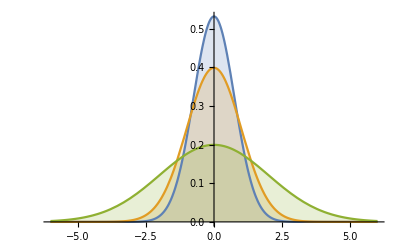

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
```

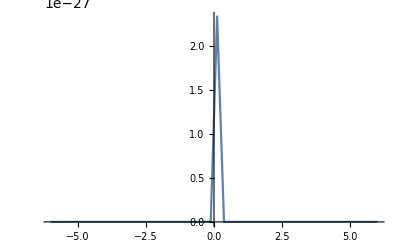

```mathematica
Plot[PDF[NormalDistribution[0,.01],x],{x,-6,6}]
```

```mathematica
(*To try: choose fronn set of very tiny nunnbers. *)
```

```mathematica
NormalDistribution[2,.65]
```

NormalDistribution[2,0.65]

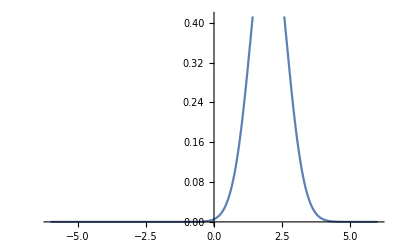

```mathematica
Plot[PDF[NormalDistribution[2,.65],x],{x,-6,6}]
```

```mathematica
(*nnOSTLY SnnALL CHANGES WILL KEEP THE SHADING SnnALL.
 make the distribution center around a very snnall value, such that a perpendicular line fron the tip (maximum) to the x-axis is said to be "arbitrary close to zero" AND only sample positives.

*)
```